```mathematica
SetDirectory["/Users/gerardoalvarez/Desktop/Inelastic Dark Matter"]
```

/Users/gerardoalvarez/Desktop/Inelastic Dark Matter

```mathematica
fileread1=OpenRead["Ine_DM_XSect_Data_Chi_10-4-0.001"];
dataread1=Read[fileread1];
Close[fileread1]

fileread2=OpenRead["Ine_DM_XSect_Data_Chi_40-7-0.003"];
dataread2=Read[fileread2];
Close[fileread2]

fileread3=OpenRead["Ine_DM_XSect_Data_Chi_160-2-0.005"];
dataread3=Read[fileread3];
Close[fileread3]

(* fileread4=OpenRead["Ine_DM_XSect_Data_Chi_160-2-10"];
dataread4=Read[fileread4];
Close[fileread4] *)
```

Ine_DM_XSect_Data_Chi_10-4-0.001

Ine_DM_XSect_Data_Chi_40-7-0.003

Ine_DM_XSect_Data_Chi_160-2-0.005

```mathematica
dataapp1=dataread1;

dataapp2=dataread2;

dataapp3=dataread3;

(* dataapp4=dataread4; *)
```

```mathematica
refdata1a=Table[{Extract[Extract[dataapp1,i],1],Extract[Extract[Extract[Extract[dataapp1,i],2],1],1]},{i,1,Length[dataapp1]}];
refdata1b=Table[{Extract[Extract[dataapp1,i],1],Re[ Extract[Extract[Extract[Extract[dataapp1,i],2],2],1]]},{i,1,Length[dataapp1]}];

refdata2a=Table[{Extract[Extract[dataapp2,i],1],Extract[Extract[Extract[Extract[dataapp2,i],2],1],1]},{i,1,Length[dataapp2]}];
refdata2b=Table[{Extract[Extract[dataapp2,i],1],Re[ Extract[Extract[Extract[Extract[dataapp2,i],2],2],1]]},{i,1,Length[dataapp2]}];

refdata3a=Table[{Extract[Extract[dataapp3,i],1],Extract[Extract[Extract[Extract[dataapp3,i],2],1],1]},{i,1,Length[dataapp3]}];
refdata3b=Table[{Extract[Extract[dataapp3,i],1],Re[ Extract[Extract[Extract[Extract[dataapp3,i],2],2],1]]},{i,1,Length[dataapp3]}];

(* refdata4a=Table[{Extract[Extract[dataapp4,i],1],Extract[Extract[Extract[Extract[dataapp4,i],2],1],1]},{i,1,Length[dataapp4]}];
refdata4b=Table[{Extract[Extract[dataapp4,i],1],Re[ Extract[Extract[Extract[Extract[dataapp4,i],2],2],1]]},{i,1,Length[dataapp4]}]; *)
```

```mathematica
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.004]}},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.004]}},{i,min10,max10},{k,9}],1]]];
```

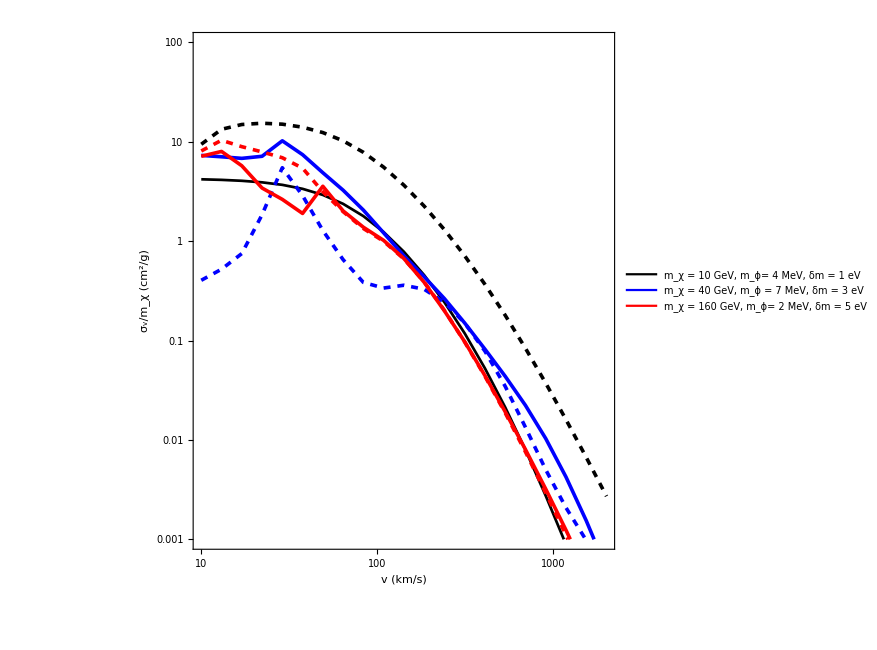

```mathematica
ListLogLogPlot[{refdata1a,refdata1b,refdata2a,refdata2b,refdata3a,refdata3b},PlotRange->{{10,2000},{ 10^-3,100}},PlotStyle-> {{Black,Thickness[0.003]},{Black,Dashed,Thickness[0.004]},{Blue,Thickness[0.004]},{Blue,Dashed,Thickness[0.004]},{Red,Thickness[0.004]},{Red,Dashed,Thickness[0.004]}},Joined->True,Frame->True,FrameLabel-> {"v (km/s)","σ_v/m_χ (cm^2/g)"},LabelStyle->Directive[Black,FontSize-> 18],FrameTicks->{{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}},PlotLegends-> Placed[LineLegend[{Black,Blue,Red},{"m_χ = 10 GeV, m_ϕ= 4 MeV, δm  = 1 eV","m_χ = 40 GeV,  m_ϕ = 7 MeV,  δm = 3 eV","m_χ = 160 GeV,  m_ϕ= 2 MeV,  δm = 5 eV "},LegendLayout->"Column"],{0.36,0.17}],FrameStyle-> Directive[Thickness[0.004],Black,FontSize-> 20],ImageSize->650,AspectRatio->1]
```

```mathematica
f
```

```mathematica
fileread1=OpenRead["Ine_DM_XSect_Data_Chi_0.010-0.0008-0.01"];
dataread1=Read[fileread1];
Close[fileread1]

fileread2=OpenRead["Ine_DM_XSect_Data_Chi_0.040-0.004-0.02"];
dataread2=Read[fileread2];
Close[fileread2]

fileread3=OpenRead["Ine_DM_XSect_Data_Chi_0.160-0.025-0.04"];
dataread3=Read[fileread3];
Close[fileread3]

fileread4=OpenRead[(*"Ine_DM_XSect_Data_Chi_0.500-20-950"*)"Ine_DM_XSect_Data_Chi_0.040-0.004-20"];
dataread4=Read[fileread4];
Close[fileread4]
```

Ine_DM_XSect_Data_Chi_0.010-0.0008-0.01

Ine_DM_XSect_Data_Chi_0.040-0.004-0.02

Ine_DM_XSect_Data_Chi_0.160-0.025-0.04

Ine_DM_XSect_Data_Chi_0.040-0.004-20

```mathematica
dataapp1=dataread1;

dataapp2=dataread2;

dataapp3=dataread3;

dataapp4=dataread4 ;
```

```mathematica
refdata1a=Table[{Extract[Extract[dataapp1,i],1],Extract[Extract[Extract[Extract[dataapp1,i],2],1],1]},{i,1,Length[dataapp1]}];
refdata1b=Table[{Extract[Extract[dataapp1,i],1],Re[ Extract[Extract[Extract[Extract[dataapp1,i],2],2],1]]},{i,1,Length[dataapp1]}];

refdata2a=Table[{Extract[Extract[dataapp2,i],1],Extract[Extract[Extract[Extract[dataapp2,i],2],1],1]},{i,1,Length[dataapp2]}];
refdata2b=Table[{Extract[Extract[dataapp2,i],1],Re[ Extract[Extract[Extract[Extract[dataapp2,i],2],2],1]]},{i,1,Length[dataapp2]}];

refdata3a=Table[{Extract[Extract[dataapp3,i],1],Extract[Extract[Extract[Extract[dataapp3,i],2],1],1]},{i,1,Length[dataapp3]}];
refdata3b=Table[{Extract[Extract[dataapp3,i],1],Re[ Extract[Extract[Extract[Extract[dataapp3,i],2],2],1]]},{i,1,Length[dataapp3]}];

refdata4a=Table[{Extract[Extract[dataapp4,i],1],Extract[Extract[Extract[Extract[dataapp4,i],2],1],1]},{i,1,Length[dataapp4]}];
refdata4b=Table[{Extract[Extract[dataapp4,i],1],Re[ Extract[Extract[Extract[Extract[dataapp4,i],2],2],1]]},{i,1,Length[dataapp4]}];
```

```mathematica
PowerTicks2[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.004]}},{i,min10,max10,2}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.004]}},{i,min10,max10},{k,9}],1]]];
```

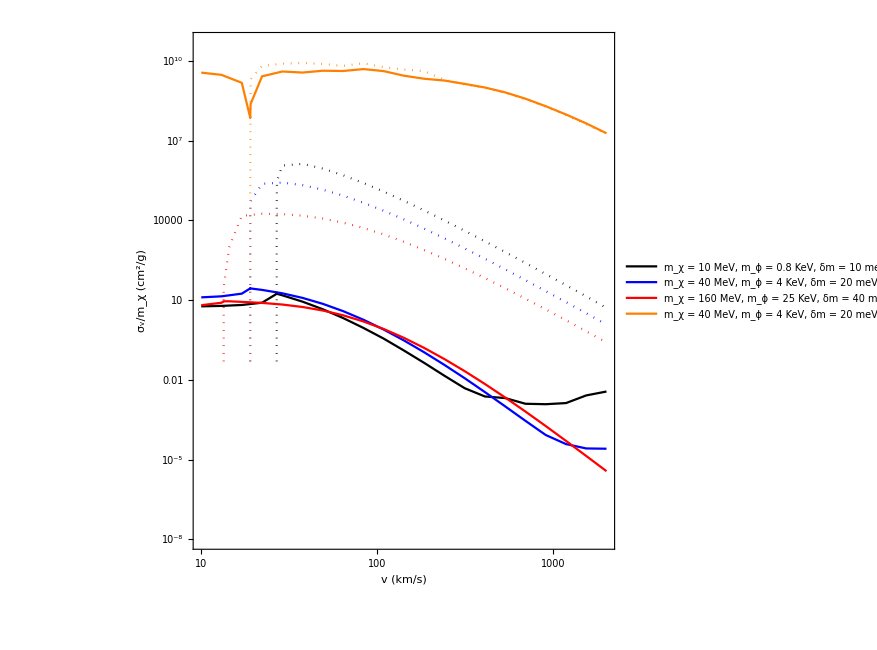

```mathematica
Show[ListLogLogPlot[{refdata1a,refdata2a,refdata3a,refdata4a},PlotRange->{{10,2000},{ 10^-8,5 10^10}},PlotStyle-> {{Black},{Blue},{Red},{Orange}},Joined->True,Frame->True,FrameLabel-> {"v (km/s)","σ_v/m_χ (cm^2/g)"},LabelStyle->Directive[Black,FontSize-> 18],FrameTicks->{{PowerTicks2[True],Automatic},{PowerTicks[True],Automatic}},PlotLegends-> Placed[LineLegend[{Black,Blue,Red,Orange},{"m_χ = 10 MeV, m_ϕ = 0.8 KeV, δm = 10 meV ","m_χ = 40 MeV, m_ϕ = 4 KeV, δm = 20 meV ","m_χ = 160 MeV, m_ϕ = 25 KeV, δm = 40 meV","m_χ = 40 MeV, m_ϕ = 4 KeV, δm = 20 meV, α_χ = 0.01"},LegendLayout->"Column"],{0.45,0.14}],FrameStyle-> Directive[Thickness[0.004],Black,FontSize-> 20],ImageSize->650,AspectRatio->1],ListLogLogPlot[{refdata1b,refdata2b,refdata3b,refdata4b},PlotRange->{{10,2000},{ 5 10^-2,5 10^10}},PlotStyle->{{Black,Dotted},{Blue,Dotted},{Red,Dotted},{Orange,Dotted}},Joined->True]]
```

```mathematica
fileread1=OpenRead["Ine_DM_XSect_Data_Chi_51-1-150"];
dataread1=Read[fileread1];
Close[fileread1]

fileread2=OpenRead["Ine_DM_XSect_Data_Chi_110-1-150"];
dataread2=Read[fileread2];
Close[fileread2]

fileread3=OpenRead["Ine_DM_XSect_Data_Chi_140-1-150"];
dataread3=Read[fileread3];
Close[fileread3]

(* fileread4=OpenRead["Ine_DM_XSect_Data_Chi_Star_180-1.5-150"];
dataread4=Read[fileread4];
Close[fileread4] *)
```

Ine_DM_XSect_Data_Chi_51-1-150

Ine_DM_XSect_Data_Chi_110-1-150

Ine_DM_XSect_Data_Chi_140-1-150

```mathematica
dataapp1=dataread1;

dataapp2=dataread2;

dataapp3=dataread3;

(*  dataapp4=dataread4; *)
```

```mathematica
refdata1a=Table[{Extract[Extract[dataapp1,i],1],Extract[Extract[Extract[Extract[dataapp1,i],2],1],1]},{i,1,Length[dataapp1]}];
refdata1b=Table[{Extract[Extract[dataapp1,i],1],Re[ Extract[Extract[Extract[Extract[dataapp1,i],2],2],1]]},{i,1,Length[dataapp1]}];

refdata2a=Table[{Extract[Extract[dataapp2,i],1],Extract[Extract[Extract[Extract[dataapp2,i],2],1],1]},{i,1,Length[dataapp2]}];
refdata2b=Table[{Extract[Extract[dataapp2,i],1],Re[ Extract[Extract[Extract[Extract[dataapp2,i],2],2],1]]},{i,1,Length[dataapp2]}];

refdata3a=Table[{Extract[Extract[dataapp3,i],1],Extract[Extract[Extract[Extract[dataapp3,i],2],1],1]},{i,1,Length[dataapp3]}];
refdata3b=Table[{Extract[Extract[dataapp3,i],1],Re[ Extract[Extract[Extract[Extract[dataapp3,i],2],2],1]]},{i,1,Length[dataapp3]}];

(* refdata4a=Table[{Extract[Extract[dataapp4,i],1],Extract[Extract[Extract[Extract[dataapp4,i],2],1],1]},{i,1,Length[dataapp4]}];
refdata4b=Table[{Extract[Extract[dataapp4,i],1],Re[ Extract[Extract[Extract[Extract[dataapp4,i],2],2],1]]},{i,1,Length[dataapp4]}]; *)
```

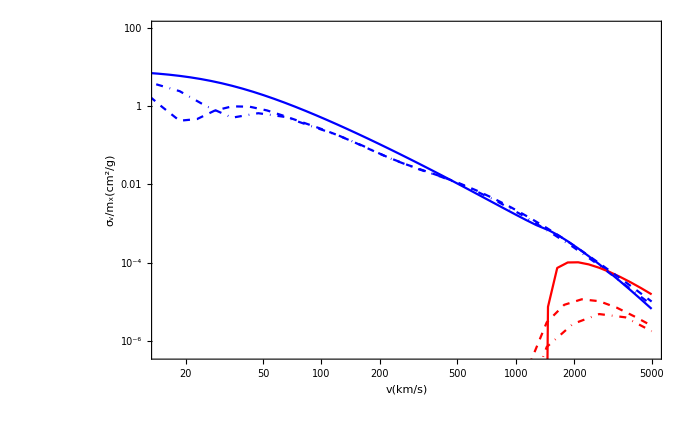

```mathematica
Show[ListLogLogPlot[refdata1a,PlotRange->{{15,5000},{5 10^-7,100}},PlotStyle-> {Blue},Joined->True],ListLogLogPlot[refdata1b,PlotStyle->{Red},Joined->True],ListLogLogPlot[refdata2a,PlotRange->{{15,5000},{5 10^-7,100}},PlotStyle-> {Blue,Dashed},Joined->True],ListLogLogPlot[refdata2b,PlotStyle->{Red,Dashed},Joined->True],ListLogLogPlot[refdata3a,PlotRange->{{15,5000},{5 10^-7,100}},PlotStyle-> {Blue,DotDashed},Joined->True],ListLogLogPlot[refdata3b,PlotStyle->{Red,DotDashed},Joined->True],(* ListLogLogPlot[refdata4a,PlotRange->{{15,5000},{5 10^-7,100}},PlotStyle-> {Blue,Dotted},Joined->True],ListLogLogPlot[refdata4b,PlotStyle->{Red,Dotted},Joined->True] , *) Frame-> True,FrameLabel-> {"v(km/s)","σ_v/m_x(cm^2/g)","δ = 150 keV"} ]
```

(erf(1-(15 √((10^x+68) 10^(y-x)))/(11 √34))+erf((15 √((10^x+68) 10^(y-x)))/(11 √34)+1)-erf(97/22)+erf(53/22))/(erf(1-(15 √(10^(-2 x) (10^x+68)^2))/(22 √17))+erf((15 √(10^(-2 x) (10^x+68)^2))/(22 √17)+1)-erf(97/22)+erf(53/22))

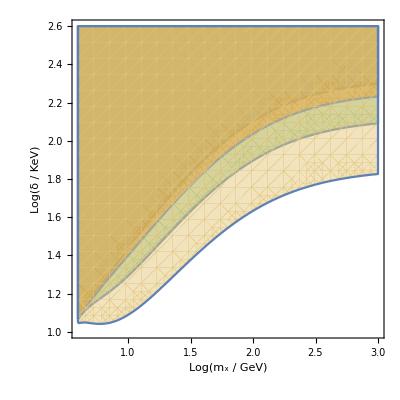

```mathematica
mA= 68  (* 122 *) ; (* Germanium / Xenon GeV *)
velocity=750/(3 10^5); (* km/s (natural units) *)
plot1=RegionPlot[ y≥Log10[1/2(10^x mA)/(10^x+mA)velocity^2 10^6  ],{x,0.6,3},{y,1,2.6},PlotStyle->Opacity[0.4]];
u0=220;
uE=220;
mb[u_]=ⅇ^(-u^2/u0^2)(ⅇ^((2u uE)/u0^2)-ⅇ^(-(2u uE)/u0^2));
Er=2 10^-6  (* 3 10^-6 *); (* Recoil threshold energy for Germanium / Xenon GeV *)
mu[x_]=(mA 10^x)/(mA+10^x);
umin[x_,y_]=√((2 10^y 10^-6 (3 10^5)^2)/mu[x]);
ur[x_]=√((mA Er(3 10^5)^2)/(2 mu[x]^2));
uesc=750;
 eta0[x_]=Integrate[mb[u],{u,ur[x],uesc}];
 eta[x_,y_]=Integrate[mb[u],{u,umin[x,y],uesc}];
 η[x_,y_]=FullSimplify[eta[x,y]/eta0[x]]
plotA=RegionPlot[η[x,y]≤  1/10,{x,0.6,3},{y,1,2.6},PlotStyle->Hue[0.12,0.44,0.9,0.5]];
plotB=RegionPlot[η[x,y]≤  1/100,{x,0.6,3},{y,1,2.6},PlotStyle->Hue[0.26,0.41,0.74,0.5]];
plotC=RegionPlot[η[x,y]≤  1/1000,{x,0.6,3},{y,1,2.6},PlotStyle->Hue[0.1,0.92,0.82,0.5]];
Show[plot1,plotB,plotC,plotA,FrameLabel-> {"Log(m_x / GeV)","Log(δ / KeV)","Ge"}]
```

```mathematica
SetDirectory["/Users/galvarez/Desktop/Xenon1T"]
```

```mathematica
fileread1=OpenRead["VelocityCurve_1MeV_1eV_2.8KeV_200_0.1"];
dataread1=Read[fileread1];
Close[fileread1]

fileread2=OpenRead["VelocityCurve_10MeV_1eV_2.8KeV_200_0.1"];
dataread2=Read[fileread2];
Close[fileread2]

fileread3=OpenRead["VelocityCurve_100MeV_1eV_2.8KeV_200_0.1"];
dataread3=Read[fileread3];
Close[fileread3]
```

VelocityCurve_1MeV_1eV_2.8KeV_200_0.1

VelocityCurve_10MeV_1eV_2.8KeV_200_0.1

VelocityCurve_100MeV_1eV_2.8KeV_200_0.1

```mathematica
dataapp1=dataread1;

dataapp2=dataread2;

dataapp3=dataread3;
```

```mathematica
refdata1a=Table[{Extract[Extract[dataapp1,i],1],Extract[Extract[Extract[Extract[dataapp1,i],2],1],1]},{i,1,Length[dataapp1]}];
refdata1b=Table[{Extract[Extract[dataapp1,i],1],Re[ Extract[Extract[Extract[Extract[dataapp1,i],2],2],1]]},{i,1,Length[dataapp1]}];

refdata2a=Table[{Extract[Extract[dataapp2,i],1],Extract[Extract[Extract[Extract[dataapp2,i],2],1],1]},{i,1,Length[dataapp2]}];
refdata2b=Table[{Extract[Extract[dataapp2,i],1],Re[ Extract[Extract[Extract[Extract[dataapp2,i],2],2],1]]},{i,1,Length[dataapp2]}];

refdata3a=Table[{Extract[Extract[dataapp3,i],1],Extract[Extract[Extract[Extract[dataapp3,i],2],1],1]},{i,1,Length[dataapp3]}];
refdata3b=Table[{Extract[Extract[dataapp3,i],1],Re[ Extract[Extract[Extract[Extract[dataapp3,i],2],2],1]]},{i,1,Length[dataapp3]}];
```

```mathematica
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.001]}},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.001]}},{i,min10,max10},{k,9}],1]]];
```

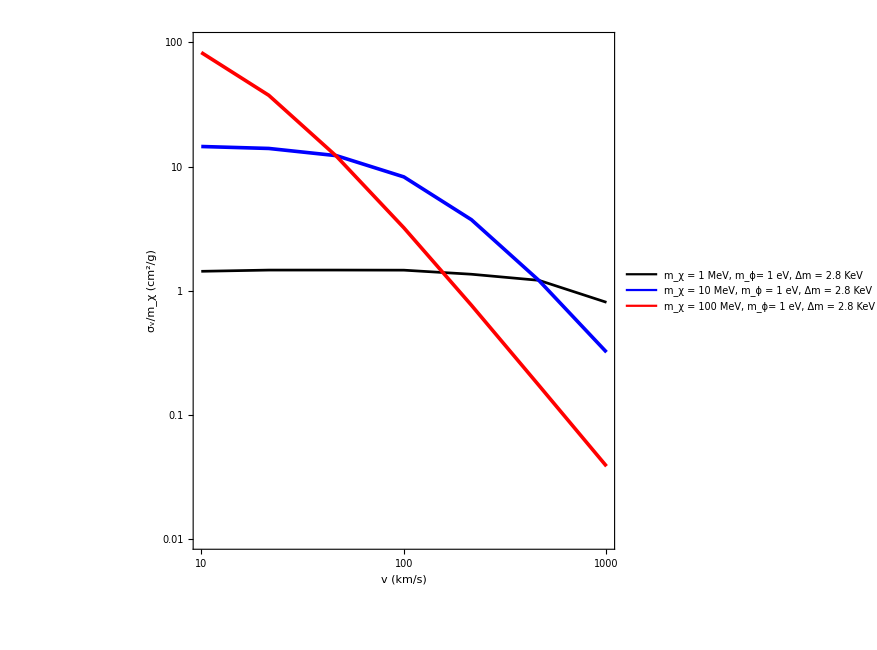

```mathematica
ListLogLogPlot[{refdata1a,refdata1b,refdata2a,refdata2b,refdata3a,refdata3b},PlotRange->{{10,1000},{ 10^-2,100}},PlotStyle-> {{Black,Thickness[0.003]},{Black,Dashed,Thickness[0.004]},{Blue,Thickness[0.004]},{Blue,Dashed,Thickness[0.004]},{Red,Thickness[0.004]},{Red,Dashed,Thickness[0.004]}},Joined->True,Frame->True,FrameLabel-> {"v (km/s)","σ_v/m_χ (cm^2/g)"},LabelStyle->Directive[Black,FontSize-> 18],FrameTicks->{{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}},PlotLegends-> Placed[LineLegend[{Black,Blue,Red},{"m_χ = 1 MeV, m_ϕ= 1 eV, Δm  = 2.8 KeV","m_χ = 10 MeV,  m_ϕ = 1 eV,  Δm = 2.8 KeV","m_χ = 100 MeV,  m_ϕ= 1 eV,  Δm = 2.8 KeV "},LegendLayout->"Column"],{0.4,0.2}],FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],ImageSize->650,AspectRatio->1]
```